# Pokrytí dat RBF sítí Demonstrace pokrytí vstupních dat složitější RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, každá třída dat se skládá ze třech dobře oddělených, shluků. Shluky se vzájemně nepřekrývají.
Vygenerujeme tyto data.

```mathematica
values=10;
cluster1x =RandomReal[{7,6},{values,1}];cluster1y=RandomReal[ {11,12},{values,1}];
cluster2x =RandomReal[{-4,-5},{values,1}];cluster2y=RandomReal[ {9,10},{values,1}];
cluster3x =RandomReal[{0,-1},{values,1}];cluster3y=RandomReal[ {12,13},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
inDataClass1 = Join[cluster1,cluster2,cluster3];
cluster4x =RandomReal[{2,1},{values,1}];cluster4y=RandomReal[ {4,5},{values,1}];
cluster5x =RandomReal[{-3,-4},{values,1}];cluster5y=RandomReal[ {12,13},{values,1}];
cluster6x =RandomReal[{9,8},{values,1}];cluster6y=RandomReal[ {10,9},{values,1}];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inDataClass2 = Join[cluster4,cluster5,cluster6];
inData= Join[inDataClass1,inDataClass2];
outClass1=ConstantArray[{1,0},{3*values}];outClass2 = ConstantArray[{0,1},{3*values}];
outData= Join[outClass1,outClass2];
```

Takto vypadají naše vynerovaná vstupní data. Můžeme je chápat jako seznam bodů, které jsou určeny svými x,y souřadnicemi.

```mathematica
inData
```

{{6.48736,11.9184},{6.0757,11.5496},{6.36352,11.7782},{6.00617,11.461},{6.8148,11.5969},{6.93043,11.6747},{6.73064,11.4738},{6.84711,11.3513},{6.60536,11.4885},{6.08589,11.9182},{-4.56111,9.29848},{-4.81159,9.03536},{-4.53692,9.25096},{-4.25474,9.34487},{-4.73425,9.42159},{-4.44218,9.23064},{-4.99709,9.51339},{-4.48178,9.06673},{-4.25322,9.82391},{-4.65152,9.61469},{-0.555867,12.6127},{-0.954568,12.1313},{-0.77126,12.8347},{-0.0645769,12.8743},{-0.802644,12.4934},{-0.566779,12.8105},{-0.22811,12.1388},{-0.0929885,12.1379},{-0.340533,12.2213},{-0.895338,12.7016},{1.49497,4.69701},{1.61974,4.20757},{1.464,4.9025},{1.41059,4.46782},{1.95422,4.4087},{1.97886,4.79538},{1.34065,4.89165},{1.34896,4.03364},{1.10073,4.09033},{1.1267,4.61007},{-3.99991,12.7559},{-3.59859,12.3037},{-3.92739,12.3492},{-3.86928,12.485},{-3.37811,12.7306},{-3.00589,12.1676},{-3.10561,12.3601},{-3.61827,12.0864},{-3.07294,12.9977},{-3.69256,12.5501},{8.24669,9.69137},{8.43384,9.25812},{8.29541,9.26412},{8.40179,9.07473},{8.43333,9.31305},{8.36341,9.82032},{8.82461,9.23576},{8.44157,9.14901},{8.16314,9.6422},{8.14116,9.53491}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme pro lepší představu zobrazit. Každá třída dat je v grafu zobrazena jinou barvou.

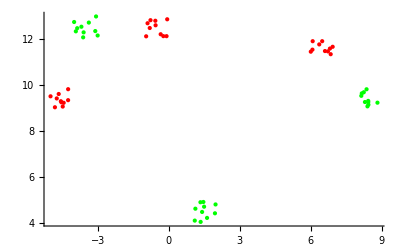

```mathematica
ListPlot[{inDataClass1,inDataClass2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě se třemi RBF neurony, dvěma vstupy a dvěma výstupními neurony.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,3,LinearPart->False,OutputNonlinearity->Sigmoid]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 21, 21, 28, 50.7769349}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme popsali.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-21 at 21:28. The network has 2 inputs and 2 outputs.  It consists of 3 basis functions of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

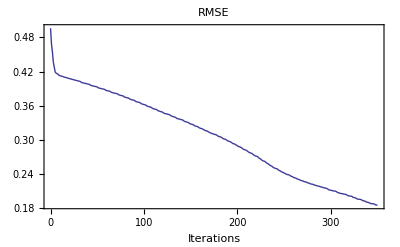

```mathematica
{net2,record}=NeuralFit[net,inData,outData,350,ReportFrequency->20];
```

Podívejme se jak naše síť klasifikuje data.

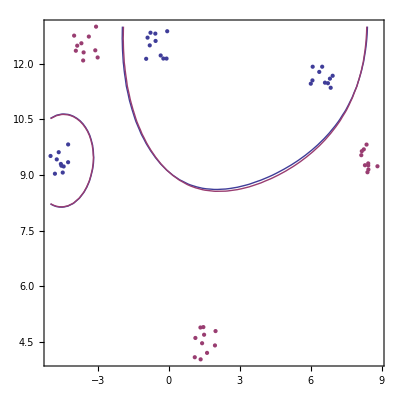

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup neuronové sítě

Podívejme se jak neuronová síť pokrývá jednotlivé třídy dat. Nejprve si zobrazíme výstup pro červenou třídu. Oblast grafu ohraničená červenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do červené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out1=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
inDataClass13d2=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
inDataClass23d2=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
data3d2=ListPointPlot3D[{inDataClass13d2,inDataClass23d2},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
out1true=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Red,Thick]];
Show[out1,out1true,data3d2]
```

-Graphics3D-

Obdobně si zobrazíme výstup pro zelenou třídu. Oblast grafu ohraničená zelenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do zelené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out2true=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Green,Thick],Mesh->None];
out2=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
Show[out2true,out2,data3d2]
```

-Graphics3D-

Obdobný výstup neuronové sítě. Do 2D jsou promítnuty hraniční přímky. Po ukázání na hraniční přímku se ukáže výstup sítě ve zormě vzorce.

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

-Graphics-

## Výstup RBF neuronů

Nyní se podíváme na “vnitřnosti” neuronové sítě. Nejprve si zobrazíme výstup všech tří RBF neuronů. Abychom se dostali k výstupu RBF neuronů musíme upravit strukturu sítě stejně jako u sítě s jedním RBF neuronem. Připojíme tedy každý RBF neuron přímo na výstupní neuron. Na výstupním neuronu se tedy zobrazí přímo hodnoty RBF neuronu.
Provedeme popsanou úpravu.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[3],{0,0,0}];(*nastaveni vystupni vrstvy*)
```

A zobrazíme výstup RBF neuronů.

```mathematica
gauss1=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All];
gauss2=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All];
gauss3=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All];
Show[gauss1,gauss2,gauss3]
```

-Graphics3D-

Výstup může mít více podob, je závislý na počáteční inicializaci sítě. Pokud vidíte pouze jednu gaussovu funkci, je možné, že ostatní jsou “pod” ní. Následující průhůedné zobrazení to objasní.

Přidáme do grafu ještě vstupní data pro lepší představu o jejich pokrytí (levé tlačítko myši otáčí graf).

```mathematica
inDataClass13d=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
inDataClass23d=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
gauss0O=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss1O=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss2O=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
data3d=ListPointPlot3D[{inDataClass13d,inDataClass23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gauss0O,gauss1O,gauss2O,data3d]
```

-Graphics3D-